# The Man Who Wanted a Wolfram Language. In 1916.

A century ago, a brilliant but unknown Englishman saw the need for a language that started with data and hence could express a world that happens from the bottom up.

James Bailey, Jun. 28,  2018

Subjects like computer programming and emergent behavior are often thought to be the province of scientists. Emergent behavior, however, happens in the parts of reality that are alive,  not the parts that are dead. So it is interesting to study a humanist who saw these phenomena a century ago and how he struggled to express what he saw. The common thread of these early thinkers is that they started their thinking with data and wanted a language that did likewise.

## “It Calls For a New Art, Yet To Be Invented”

When George Sturt, the Gregor Mendel of computational thinking, was attempting to communicate his insights back in the early 20th century, he recognized that realities like emergent behavior could not be expressed in words. He looked at the behavior of individual family members, then at the collective behavior of the family as a whole. The family behavior was different in ways that could not be expressed as the sum of the individual behaviors. He yearned for a language that could express what he saw:

“The [individual] organism doing its work, instinctively and well: and so the family, another organism, doing equally well … it does call for a new art, yet to be invented for recording such things.”

Well, that new art is being invented, although it cannot be summarized in any single line of code. So here, dear reader, just imagine a call to the whole neural network environment.

```mathematica
(* call into the neural network environment *)
```

## The New Art Starts With Data. Detailed Data.

We know that George gathered and recorded exactly the kinds of detailed data that now come for free in the online world:

“I was counting up last night the elemental tragedy stuff that has occurred in the cottages within 100 yards from here, since I came here seven years ago: 4 deaths of old men, 2 deaths of young men leaving families, 1 death of a mother, 1 death of an infant, 1 case of sunstroke, with delirium, 1 case of hemorrhage with fits, and 1 girl home 'in trouble.'”

```mathematica
(* we start with the data *)
neighborEventsList:={"death of old man","death of old man","death of old man","death of old man",
"death of young man leaving family","death of young man leaving family","death of an infant",
"case of sunstroke,with delirium","case of hemorrhage with fits","girl home in trouble"}
```

## But To Let the Data Tell Its Story, We Need Lots Of It.

“I don’t want heroics, but most details have a trick of looking petty until they can be seen as part of an immense lump which dignifies them.”

```mathematica
(* imagine a contemporary dataset with 500,000+ training examples *)
neighborEventsList := { "death of old man" , "death of old man" , "death of old man" , "death of old man" , "death of young man leaving family" , 
"death of young man leaving family" , "death of an infant" , "case of sunstroke, with delirium" , "<<500000>>" , "case of hemorrhage with fits" , "girl home in trouble" }
```

And notice that these two versions of the symbol “neighborEventsList” are identical in the way one can work with them. They are both just lists.

The New Art Works From the Bottom Up, Not From the Top Down.

It took a rare person to get beyond the prevailing wisdom of the day (that the world operates from the top down) and to entertain the idea that it can all happen from the  bottom up. And probably does.

“Theology starts with God creating all things, then works down to ‘mere’ dust, ‘mere’ atoms, ‘mere’ matter. And we talk of these things scornfully, as if there was nothing wonderful in them … But what if we begin at the other end? How if we acknowledge … this splendour in ‘Dust,’ in atoms, in matter, that (perhaps as outcome of its inscrutable nature) it works itself up by some unknown and unknowable urge, into Stellar universes, into Life, into Friendship, into fancy that imagines ‘God’? … and the thing that theology despises turns out to be beyond words splendid, beyond the utmost reaches of thought mysterious and beautiful.”

All too often, today’s students are introduced to genomics by the example of the cystic fibrosis gene, which has impact all by itself.

```mathematica
cysticFibrosis := List[ "CFTRgene" ];
```

That is not how genes in general work. Genetics is a world where hundreds of genes work together to have influence in multiple places.It takes an immense lump of them:

```mathematica
spatialReasoning := List[ "geneABC" , "<<100>>" , "geneXYZ" ] ;
```

Kids today need to start their thinking with long (who cares how long) lists, not with lists of just one number.

## Life Itself Is a Neural Network

Sturt understood the key element of a neural network: the intelligence is spread across the whole network; no single node has it all.

“The lore was a tangled network of country prejudices, whose reasons were known in some respects here, in others there, and so on. In farm-yard, in tap-room, at market, the details were discussed over and over again; they were gathered together for remembrance in village workshop; carters, smiths, farmers, wheel-makers, in thousands handed on each his own little bit of understanding, passing it to his son or the wheelwright of the day, linking up the centuries. But for the most part the details were but dimly understood; the whole body of knowledge was a mystery, a piece of folk knowledge, residing in the folk collectively, but never wholly in any individual.”

```mathematica
positionNodes[ nodeList_] := (
bottomMargin := 4 ; leftMargin := 4 ; topMargin := 4.5 ; rightMargin := 0 ;
graphHeight := 72 ; graphWidth := 100 ;

If[ Length[ nodeList ] < 3 ,
maxHiddenLayer := 1 ; ,
maxHiddenLayer := Max[ Part[ nodeList[ [ 2;;Length[ nodeList ] -2] ] ] ] ;
] ;
verticalGapDivisor := 5 ;
horizontalGapDivisor := 8.0 / Max[ nodeList ] ;
availableVerticalSpace := graphHeight - topMargin -bottomMargin ;
verticalNodePixels := availableVerticalSpace / Max[ nodeList ] ;
availableVerticalDiameter := verticalNodePixels * verticalGapDivisor / ( verticalGapDivisor + 1 ) ;
availableHorizontalSpace := graphWidth - leftMargin - rightMargin ;
horizontalNodePixels := availableHorizontalSpace / ( Length[ nodeList ] + 1 ) ;
availableHorizontalDiameter := horizontalNodePixels * horizontalGapDivisor / ( horizontalGapDivisor + 1 ) ;
nodeRadius:= 0.5 * Min[ availableVerticalDiameter , availableHorizontalDiameter ] ;
verticalGap := verticalNodePixels - availableVerticalDiameter ;
horizontalGap := horizontalNodePixels - nodeRadius ;
outputNodeX := Length[ nodeList ] * ( 2 * nodeRadius + ( 2 / horizontalGapDivisor ) *nodeRadius ) ;
horizontalIndent := 0.5 * ( graphWidth - outputNodeX + leftMargin ) ;

If[ Length[ nodeList ] == 3 ,
verticalIndents := { 0 , 18 , 18 } ,
(
verticalIndents := {} ;
For[i=1,i<=Length[ nodeList ],i++,
thisHiddenLayerNodeCount := nodeList[[ i  ]] ;
thisHiddenLayerVerticalExtent := 2 * nodeRadius * thisHiddenLayerNodeCount + verticalGap * ( thisHiddenLayerNodeCount - 1 ) ;
thisVerticalIndent := topMargin + 0.5 * ( graphHeight - topMargin - bottomMargin - thisHiddenLayerVerticalExtent ) ;
AppendTo[  verticalIndents , thisVerticalIndent  ] ;
] ;
) ;
] ;

nodesXY := { } ;
inputNodes := {} ;
hiddenNodes := {} ;
ouputNodes := {} ;
For[ overallLayers = 1 , overallLayers <= Length[ nodeList ] , overallLayers++ ,
For[ nodesInThisLayer = 1 , nodesInThisLayer <= nodeList[[ overallLayers  ]] , nodesInThisLayer++,
tempDouble := ( overallLayers - 1 ) * ( 2 * nodeRadius + ( 2.0 / horizontalGapDivisor ) * nodeRadius ) ;
thisNodeX := horizontalIndent + tempDouble ;

If[ overallLayers == 1 && nodeList[[1]] > maxHiddenLayer ,
thisNodeY := topMargin + nodeRadius + ( nodesInThisLayer - 1 ) * (2 * nodeRadius + verticalGap ) ,
thisNodeY := verticalIndents[[ overallLayers ]] + nodeRadius + ( nodesInThisLayer - 1 ) * (2 * nodeRadius + verticalGap )
] ;

thisNodeXY := { { thisNodeX  , thisNodeY }  , nodeRadius  } ;
If[ overallLayers==1 , AppendTo[ inputNodes , thisNodeXY ] , , ] ;
If [overallLayers > 1 && overallLayers < Length[nodeList] - 1 , AppendTo[ hiddenNodes , thisNodeXY ] , , ] ;
If[  overallLayers >= Length[nodeList] - 1 ,AppendTo[ ouputNodes , thisNodeXY ] , , ] ;
AppendTo[ nodesXY , thisNodeXY ] ;
] ;
] ;

threeNodeTypes := {} ;
AppendTo[ threeNodeTypes , inputNodes ] ;
AppendTo[ threeNodeTypes , hiddenNodes ] ;
AppendTo[ threeNodeTypes , ouputNodes ] ;
Return[  threeNodeTypes  ] ;
)

(*********************************************************************************)

positionAllLinks[ nodesPerLayer_ , nodeCenters_]:= 
(
nodeXYs:= {} ;
nodeRadii := {} ;
For[ i = 1 , i <= Length[ nodeCenters ] , i++ ,
AppendTo[ nodeXYs , Part[ nodeCenters[[ i ]] , 1 ] ] ;
AppendTo[ nodeRadii , Part[ nodeCenters[[ i ]] , 2 ] ] ;
] ;
localLayerCounts = Prepend[ nodesPerLayer , 0 ] ;

start = 1 ;
layerCenters := {} ;
layerNodeRadii := {} ;
For[ i = 1 , i < Length[ localLayerCounts ] , i++ ,(
end = start + localLayerCounts[[ i+1  ]] - 1 ;
thislayerList := nodeXYs[[ start;;end ]] ;
AppendTo[ layerCenters , nodeXYs[[ start;;end ]]  ] ;
AppendTo[ layerNodeRadii , nodeRadii[[ start;;end ]] ] ;
start = start + localLayerCounts[[ i+1  ]] ;
)
] ;

centerToCenterXYs = {} ;
croppedInputXYs = {} ;
croppedHiddenXYs = {} ;
croppedOutputXYs = {} ;
For[ i = 1 , i <= Length[ layerCenters ] - 1 , i++ , (
sourceNodeList := layerCenters[[i]] ;
destinationNodeList := layerCenters[[i+1]] ;

For[ j = 1 , j <= Length[ sourceNodeList ] , j++ , (
For[ k=1 , k<=Length[destinationNodeList] , k++ , (

point1X := Part[ sourceNodeList[[ j]] , 1 ] ;
point1Y := Part[ sourceNodeList[[ j]] , 2 ] ;
point2X := Part[ destinationNodeList[[k]] , 1 ] ;
point2Y := Part[ destinationNodeList[[k]] , 2 ] ;
radius1 := Part[ layerNodeRadii[[i]] , 1 ] ;
radius2 := Part[ layerNodeRadii[[i]] , 1 ] ;

deltaY := point2Y - point1Y ;
deltaX := point2X - point1X ;
length := Sqrt[ deltaX * deltaX + deltaY * deltaY ] ;
r1L := radius1 / length ;
r2L := radius2 / length ;

point1Y = SetPrecision[ point1Y + deltaY * r1L, 4 ] ;
point2Y = SetPrecision[ point2Y - deltaY * r2L, 4  ] ;
point1X = SetPrecision[  point1X + deltaX * r1L, 4  ] ;
point2X = SetPrecision[ point2X - deltaX * r2L, 4  ] ;
thisCroppedXY := { { point1X , point1Y } , { point2X , point2Y } } ;

If[ i<2 , AppendTo[ croppedInputXYs , thisCroppedXY ] , ] ;
If[ i>1 && i < Length[layerCenters ] - 2 , AppendTo[ croppedHiddenXYs , thisCroppedXY ] , ] ;
If[ i>= Length[layerCenters ] - 2 , AppendTo[ croppedOutputXYs , thisCroppedXY ] , ] ;
AppendTo[ centerToCenterXYs , thisCroppedXY ] ;
)
] ;
)
] ;
)
] ;
threeLinkTypes := {} ;
AppendTo[ threeLinkTypes , croppedInputXYs ] ;
AppendTo[ threeLinkTypes , croppedHiddenXYs ] ;
AppendTo[ threeLinkTypes , croppedOutputXYs ] ;
Return[  threeLinkTypes  ] ;
)

(******************************************************************************************)

showNeuralNetwork[ nodesPerLayerList_] := (
prunedLayerList = {} ;
For[ i = 1 , i <= Length[ nodesPerLayerList ] , i++ , 
If[ nodesPerLayerList[[i]] > 0 , AppendTo[ prunedLayerList , nodesPerLayerList[[i]] ] , ] ;
] ;

splitNodeCenterList := positionNodes[ prunedLayerList ] ;
inputLayerNodes := Part[ splitNodeCenterList , 1 ] ;
hiddenLayerNodes := Part[ splitNodeCenterList , 2 ] ;
outputLayerNodes := Part[ splitNodeCenterList , 3 ] ;

inputNodesFontSize = 10.0 * nodeRadius ;
inputNodeLabels := {} ;
For[ q=1 , q <= Length[  inputLayerNodes ], q++ ,
thisNodeLayer = Part[ inputLayerNodes[[q]] , 1 ] ;
thisNodeLayerXY = { Part[ thisNodeLayer , 1  ] ,  Part[ thisNodeLayer , 2  ] - nodeRadius / 7.0 } ;
AppendTo[ inputNodeLabels , { "X" , thisNodeLayerXY }  ] ;
] ;

hiddenNodesFontSize = 10.0 * nodeRadius ;
hiddenNodeLabels := {} ;
For[ r=1 , r <= Length[  hiddenLayerNodes ], r++ ,
thisNodeLayer = Part[ hiddenLayerNodes[[r]] , 1 ] ;
thisNodeLayerXY = { Part[ thisNodeLayer , 1  ] ,  Part[ thisNodeLayer , 2  ] - nodeRadius / 7.0 } ;
AppendTo[ hiddenNodeLabels , { "A" , thisNodeLayerXY } ]
];

outputNodesFontSize = 10.0 * nodeRadius ;
outputNodeLabels := {} ;
For[ s=1 , s <= Length[  outputLayerNodes ], s++ ,
thisNodeLayer = Part[ outputLayerNodes[[s]] , 1 ] ;
thisNodeLayerXY = { Part[ thisNodeLayer , 1  ] ,  Part[ thisNodeLayer , 2  ] - nodeRadius / 7.0 } ;
If[ s==1 ,
AppendTo[ outputNodeLabels , { "A" , thisNodeLayerXY } ] ,
AppendTo[ outputNodeLabels , { "Y" , thisNodeLayerXY } ]
] ;
];
hatFontSize = 18.0 * nodeRadius ;
thisNodeLayer = Part[ outputLayerNodes[[2]] , 1 ] ;
thisNodeLayerXY = { Part[ thisNodeLayer , 1  ] + nodeRadius / 10.0 ,  Part[ thisNodeLayer , 2  ] - nodeRadius / 4.4 } ;
hatLabel = { { "ˆ" , thisNodeLayerXY } } ;

nodeCenterList := Join[ inputLayerNodes , hiddenLayerNodes , outputLayerNodes ] ;
tripleNetworkLinks := positionAllLinks[prunedLayerList , nodeCenterList] ;
inputLayerLinks := Part[ tripleNetworkLinks , 1 ] ;
hiddenLayerLinks := Part[ tripleNetworkLinks , 2 ] ;
outputLayerLinks := Part[ tripleNetworkLinks , 3 ] ;

Graphics[{ Thick , Arrowheads[Medium] ,
Magenta , Arrow /@ inputLayerLinks , 
Gray , Arrow /@ hiddenLayerLinks , 
Blue , Arrow /@ outputLayerLinks  , 

EdgeForm[{Magenta, Thick}], FaceForm[LightMagenta], Disk @@@ inputLayerNodes , 
EdgeForm[{Gray, Thick}], FaceForm[LightGray],Disk @@@ hiddenLayerNodes , 
EdgeForm[{Blue, Thick}],, FaceForm[LightBlue] , Disk @@@ outputLayerNodes  , 

Magenta ,FontSize-> inputNodesFontSize , Text @@@ inputNodeLabels ,
Black ,FontSize-> hiddenNodesFontSize , Text @@@ hiddenNodeLabels ,
Blue ,FontSize-> outputNodesFontSize , Text @@@ outputNodeLabels ,
Blue ,FontSize-> hatFontSize , Text @@@ hatLabel

}, 
ImageSize->Full]

) ;
```

```mathematica
(* change the list to change the shape of the neural network *)
(* (assuming you have evaluated eveything to this point) *)
```

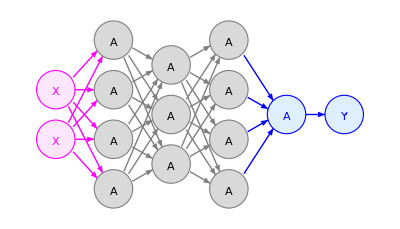

```mathematica
showNeuralNetwork[ { 2 , 4  , 3 ,  4 , 1 , 1   } ]
```

## Author contact information

bailey@selfschooling.com

## Guidelines for the Author

### Image

### Text

### Code